## Parameters

```mathematica
L = 4;
J = 1;
tMax=100;
tPts=50;
Prec=40;
tVals = N[Table[tMax*(i)/(tPts), {i, 1, tPts}], Prec];
```

## Functions to take tensor products of local operators

```mathematica
(*Given a binary number occupation rep of spins, it gives the corresponding matrix by taking a tensor product along the chain*)
ChainOccRepTensorProduct[OccRep_, Spin_] := Module[{a}, 
a=IdentityMatrix[1];
Do[ If[OccRep[[i]]==0, a = KroneckerProduct[a,IdentityMatrix[Dimensions[Spin]]]];
If[OccRep[[i]]==1, a = KroneckerProduct[a, Spin]];
,{i, 1, Length[OccRep]}];
a]
```

```mathematica
(*Takes Tensor product along the chain, with operator at position Position, and identities everywhere else*)
ChainTensorProduct[Length_,Operator_,Position_]:=Module[{list,chain},
list=ConstantArray[IdentityMatrix[2],Length];list[[Position]]=Operator;
chain=Apply[KroneckerProduct,list]]
```

```mathematica
(*Takes Tensor product along the chain, with operators at position Position and Position +1, and identities everywhere else*)
ChainNeighbourTensorProduct[Length_,Operator1_,Operator2_,Position_,PBC_:False]:=Module[{list,chain}, 
list=ConstantArray[IdentityMatrix[2],Length];
If[Position==Length, list[[Position]]=Operator1;list[[1]]=Operator2,list[[Position]]=Operator1;list[[Position+1]]=Operator2];
chain=Apply[KroneckerProduct,list]]
```

```mathematica
JordanWignerTensorProduct[Length_,StringOperator_,Operator_,Position_]:=Module[{list,chain},
list=Join[ConstantArray[StringOperator,Position-1],{Operator},ConstantArray[IdentityMatrix[2],Length-Position]];
chain=Apply[KroneckerProduct,list]]
```

## Functions to calculate Lanczos Coefficients

```mathematica
comm[Op1_,Op2_]:= Module[{com},com= Op1 . Op2 - Op2 . Op1]
```

```mathematica
DocInnerProd[A_,B_] := Module[{psi},psi=Conjugate[Flatten[A]] . Flatten[B]]
```

```mathematica
LanczosDoc[H_,S_,nmax_,precision_,btol_,bPrecision_] := Module[{b,Op1,Op2,Op3,B,LOp ,NormSq1,NormSq2,tolval, count,OpDim, i,Ops},
(*In order to improve efficiency we initialize and pre-allocate arrays of length nmax to prevent dynamic resizing of arrays in the loop*)
(*Op and LOp are arrays of matrices which are the dimension of S*)
count=1;
b=ConstantArray[0.,nmax];
Ops=ConstantArray[0.,{nmax,Length[H],Length[H]}];

Op1=N[S,precision];
LOp=comm[H,Op1];
NormSq1=DocInnerProd[Op1,Op1];
Op2=LOp;

Do[(*A couple of dummy variables, to reduce repeat calculations. Worse space efficiency though*)
LOp=comm[H,Op2];
NormSq2=DocInnerProd[Op2,Op2];
B=DocInnerProd[Op1,LOp];
tolval=B/NormSq1;
Op3=LOp-tolval*Op1;

(*If[Precision[tolval]<2,Print["Precision of tolval is less than 2"]];*)
If[N[tolval]<btol,Print["Cut-off reached at n= ",i,", since tolval (\!\(\*FractionBox[\(b[i]\), \(NormSq[i - 1]\)]\)) and btol are ",tolval," and ",btol]; 
(* Break when the (approximate) Lanczos coefficients reach close to zero. We want to catch this and break before we hit a div by zero error in the b[[i]]*)
Break[]];
b[[i]]=N[B/Sqrt[NormSq1*NormSq2],bPrecision];
Ops[[i]]=Op1;

Op1=Op2;
Op2=Op3;
NormSq1=NormSq2;

count++;
(*If[Mod[count,100]==0,Print["Count is: ",count]];*)
,{i,2,nmax}];
{Table[b[[i]],{i,1,count}],Table[Ops[[i]],{i,1,count}]}]
```

```mathematica
(*Generate set with repeated actions of Liouvillian on state Op*)
InitialBasis[H_,Op_,n_,prec_]:=
Module[{B},B=N[NestList[comm[H,#]&,Op,n],prec]]
```

```mathematica
(*Generate Othogonal Basis*)
OrthoBasis[H_,Op_,n_,prec_]:=
Module[{B},B=Orthogonalize[InitialBasis[H,Op,n-1,prec],DocInnerProd, Method->"GramSchmidt",Tolerance->10^(-10)]]
```

```mathematica
(*Extract b_ns from the off-diagonals of the Louivillian in the Krylov Basis*)
LanczosOrthog[H_,Op_,nmax_,prec_]:=
Module[{B,a,b},
B=OrthoBasis[H,Op,nmax,prec];
a=Table[DocInnerProd[B[[n]],comm[H,B[[n]]]],{n,1,nmax-1}];
b=Table[DocInnerProd[B[[n-1]],comm[H,B[[n]]]],{n,2,nmax-1}];
{a,b}]
```

## Functions to make Matrices for Ising Chain Hamiltonian and Operators

```mathematica
HIsingIntMode[n_]:=-J*ChainNeighbourTensorProduct[L,PauliMatrix[3],PauliMatrix[3],n];
HIsingBMode[n_]:=-J*ChainTensorProduct[L,PauliMatrix[1],n];
```

```mathematica
HIsing = Sum[HIsingIntMode[n],{n,1,L-1}]+Sum[HIsingBMode[n],{n,1,L}];
MatrixForm[HIsing]
HIsingNormed = HIsing/Sqrt[DocInnerProd[HIsing,HIsing]];
```

(-2 | -1 | -1 | 0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | -1 | 0 | -1 | 0 | 0
-1 | 0 | 2 | -1 | 0 | 0 | -1 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | -1 | 0 | 0 | -1 | 2 | 0 | -1
0 | 0 | -1 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | -1 | 0 | -1 | -1 | -2)

### Operators

```mathematica
σPlus0={{0,1},{0,0}};
σMinus0={{0,0},{1,0}};
```

```mathematica
σzMode[n_] := ChainTensorProduct[L, PauliMatrix[3], n];
σyMode[n_] := ChainTensorProduct[L, PauliMatrix[2], n];
σxMode[n_] := ChainTensorProduct[L, PauliMatrix[1], n];
σPlusMode[n_] := ChainTensorProduct[L, σPlus0, n];
σMinusMode[n_] := ChainTensorProduct[L, σMinus0, n];
```

```mathematica
σz = Sum[σzMode[n],{n,1,L}]
σy = Sum[σyMode[n],{n,1,L}];
σx = Sum[σxMode[n],{n,1,L}];
σPlus = Sum[σPlusMode[n],{n,1,L}]; 
σMinus = Sum[σMinusMode[n],{n,1,L}];
```

{{3,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-3}}

### Non-local Operators

c_i= Π_(j<i)(σ^z)_j(σ^-)_i
(c^+)_i= Π_(j<i)(σ^z)_j(σ^+)_i

```mathematica
ccMode[n_]:=JordanWignerTensorProduct[L,PauliMatrix[3],σMinus0,n];
cdMode[n_]:=JordanWignerTensorProduct[L,PauliMatrix[3],σPlus0,n];
```

```mathematica
ccc=Sum[ccMode[n],{n,1,L}];
cdc = Sum[cdMode[n], {n, 1, L}];
MatrixForm[ccc]
MatrixForm[cdc]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | -1 | 0)

(0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Function to calculate the Return Amplitude (Inputs: H, Operator)

```mathematica
NormalizedReturnAmplitude[H_, Operator_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
U=Refine[MatrixExp[-I*t*H],t ∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U].Operator.U ,t ∈Reals];
NNNexpr = FullSimplify[Expand[DocInnerProd[Operator,EvolvedOperator]],t ∈Reals];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
FasterReturnAmp[H_,Operator_,NPrec_, ChopTol_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Chop[Refine[Inverse[vecs] . MatrixExp[I*t*DiagonalMatrix[vals]] . vecs,t∈Reals],ChopTol];
EvolvedOperator=ConjugateTranspose[U] . Refine[Operator . U,t∈Reals];
NNNexpr=FullSimplify[Chop[DocInnerProd[Operator,EvolvedOperator],ChopTol], Assumptions->{t∈Reals}];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
FastReturnAmp[H_,Operator_,NPrec_]:=Module[{U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Refine[Inverse[vecs] . MatrixExp[I*t*DiagonalMatrix[vals]] . vecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
(*Print[DocInnerProd[Operator,EvolvedOperator]];*)
InnProd=DocInnerProd[Operator,EvolvedOperator];
NNNexpr=Simplify[InnProd];
(*Print[NNNexpr];*)
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
FastReturnAmpMessy[H_,Operator_,NPrec_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Refine[Inverse[vecs] . MatrixExp[I*t*DiagonalMatrix[vals]] . vecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
NNNexpr=DocInnerProd[Operator,EvolvedOperator];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
FastReturnAmpFrac[H_,Operator_,NPrec_]:=Module[{U,EvolvedOperator,InnProd,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
Nvals=N[vals,NPrec];Nvecs=N[vecs,NPrec];
CutVals=Table[x=Nvals[[i]];If[IntegerPart[x]==x,x=IntegerPart[x],x],{i,1,Length[Nvals]}];
FracVals=Last[Convergents[CutVals[[#]]]]&/@Range[Length@CutVals];
CutVecs=Table[x=Nvecs[[i,j]];If[IntegerPart[x]==x,x=IntegerPart[x],x],{i,1,Length[Nvecs]}, {j,1,Length[Nvecs]}];
FracVecs= Table[Last[Convergents[CutVecs[[i,j]]]],{i,1,Length[CutVecs]}, {j,1,Length[CutVecs]}];
U=Refine[Inverse[FracVecs] . MatrixExp[I*t*DiagonalMatrix[FracVals]] . FracVecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U] . Operator . U,t∈Reals];
InnProd=DocInnerProd[Operator,EvolvedOperator];
NNNexpr=Simplify[InnProd];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
ExactReturnAmp[H_,Operator_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
U=Refine[Inverse[vecs] . MatrixExp[I*t*DiagonalMatrix[vals]] . vecs,t∈Reals];
EvolvedOperator=ConjugateTranspose[U] . Refine[Operator . U,t∈Reals];
NNNexpr=FullSimplify[DocInnerProd[Operator,EvolvedOperator], Assumptions->{t∈Reals}];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

## Function to calculate Amplitude Coefficients (Inputs: as,bs,ReturnAmp,tvals,prec)

```mathematica
AmplitudeCoefficient[as_,bs_,ReturnAmp_,tVals_,Prec_]:=Module[{ϕPts,NNND,NNNDTab,Genf,FtoNSwap,ϕt,cc,PTab},
 ϕPts = Length[bs];
(*"Here the derivatives are computed at the time-points.  "*)
	 NNND[0] = ReturnAmp;
	Do[NNND[j+1] =  D[NNND[j], t]    , {j, 0, ϕPts}  ];
	NNNDTab = Table[NNND[j]/.t->tVals, {j, 0, ϕPts}];
	Genf=F[t];
	(*"The substitution to the function F(t)"*)
	FtoNSwap = Table[D[F[t], {t,k}] -> NNNDTab[[k+1]], {k, 0, ϕPts}];
	 ϕt = Table[D[ Genf  , {t, k}], {k, 0, ϕPts}]/.FtoNSwap;
(*"Here we compute the coefficeints cc "*)
	Clear[cc];   cc[0,0]=1; cc[0,-1] = 0;
(*CHANGED TO HAVE N ONLY GO TO ϕPts-1*)
Do[  cc[m,n+1]  = N[(If[m≥ 1, I*cc[m-1,n], 0]  +If[m≤ n, as[[n+1]]*cc[m,n], 0]   - If[m≤n -1&& n>0, bs[[n]]*cc[m,n-1] , 0 ])/bs[[n+1]], Prec]  , {n, 0, ϕPts-1}, {m, 0, n+1}]; 
PTab = Table[  Sum[ N[N[cc[m,kk], Prec]*ϕt[[m+1]], Prec], {m, 0, kk}] , {kk, 0, ϕPts}]]
```

## Function to calculate Komplexity

```mathematica
NormKComplexityFromBs[b_,bmax_,tmax_]:=Module[{ϕ,soln,bNew, bSlice,f,K,NormK},
(*Solve the particle hopping equation with Zero BC on n, and IC of Subscript[ϕ, n](0)= Subscript[δ, n](0)*)
bNew=Prepend[b,0];
bNew=bNew[[;;bmax+1]];
bNew= Append[bNew,0];
soln=NDSolve[Join[Table[D[ϕ[n,t],t]==
 bNew[[n+1]]*ϕ[n-1,t]- bNew[[n+2]]*ϕ[n+1,t],{n,0,bmax}],
Table[ϕ[n,0]==KroneckerDelta[n,0],{n,0,bmax}]],{Table[ϕ[n,t],{n,0,bmax}]},{t,0,tmax}];
(*Extract the phi's from the solution*)
f=soln[[1]][[1]][[2]];
(*Calculate the Normalized K-Complexity from the phi's*)
NormK=Sum[n*Conjugate[f[[n+1]]]*f[[n+1]],{n,1,bmax}]/Sum[Conjugate[f[[n+1]]]*f[[n+1]],{n,1,bmax}]
]
```

```mathematica
NormKComplexityFromAsAndBs[a_,b_,bmax_,tmax_]:=Module[{ϕ,soln,aNew,bNew, bSlice,f,K,NormK},
(*Solve the particle hopping equation with Zero BC on n, and IC of Subscript[ϕ, n](0)= Subscript[δ, n](0)*)

bNew=Prepend[b,0];
aNew=a[[;;bmax+1]];
bNew=bNew[[;;bmax+1]];
bNew= Append[bNew,0];

soln=NDSolve[Join[Table[D[ϕ[n,t],t]==
-I*aNew[[n+1]]+ bNew[[n+1]]*ϕ[n-1,t]- bNew[[n+2]]*ϕ[n+1,t],{n,0,bmax}],
Table[ϕ[n,0]==KroneckerDelta[n,0],{n,0,bmax}]],{Table[ϕ[n,t],{n,0,bmax}]},{t,0,tmax}];
(*Extract the phi's from the solution*)
f=soln[[1]][[1]][[2]];
(*Calculate the Normalized K-Complexity from the phi's*)
NormK=Sum[n*Conjugate[f[[n+1]]]*f[[n+1]],{n,1,bmax}]/Sum[Conjugate[f[[n+1]]]*f[[n+1]],{n,1,bmax}]
]
```

```mathematica
{as,bs}={{0,1,2,3,4,5,1,1,1},{0,√2,√2,0,2 ⅈ,ⅈ √10,3 ⅈ √2,2 ⅈ √7}};
```

```mathematica
NormK=NormKComplexityFromAsAndBs[as,Delete[bs,1],6,10];
Plot[NormK,{t,0,10}]
```

{√2,√2,0,2 ⅈ,ⅈ √10,3 ⅈ √2,2 ⅈ √7}

{0,√2,√2,0,2 ⅈ,ⅈ √10,3 ⅈ √2,2 ⅈ √7}

{0,√2,√2,0,2 ⅈ,ⅈ √10,3 ⅈ √2,0}{8}

-Graphics-

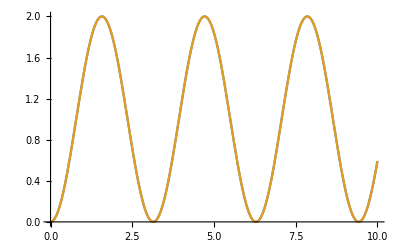

```mathematica
NormK=NormKComplexityFromBs[bs,4,10];
Plot[{NormK,2(Sin[t]^2)},{t,0,10}]
```

## Testing how truncation of Lanczos coefficients affects support for various operators

### Simple Ops

```mathematica
H=HIsingBMode[1]+HIsingIntMode[1]
Op=σxMode[1]
```

{{-1,0,0,0,-1,0,0,0},{0,-1,0,0,0,-1,0,0},{0,0,1,0,0,0,-1,0},{0,0,0,1,0,0,0,-1},{-1,0,0,0,1,0,0,0},{0,-1,0,0,0,1,0,0},{0,0,-1,0,0,0,-1,0},{0,0,0,-1,0,0,0,-1}}

{{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}}

```mathematica
ReturnAmpLocal=ExactReturnAmp[H,Op]
```

Cos[√2 t]^2

```mathematica
{as,bs}=LanczosOrthog[H,Op,4,20]
```

{{0.,0.,0.},{2.,2.}}

```mathematica
PTabLocal=AmplitudeCoefficient[as,bs,ReturnAmpLocal,tVals,Prec];
```

```mathematica
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabLocal[[k, j]]^2 ] , {k, 1, Length[PTabLocal]} ] }, {j, 1, Length[tVals]}];
```

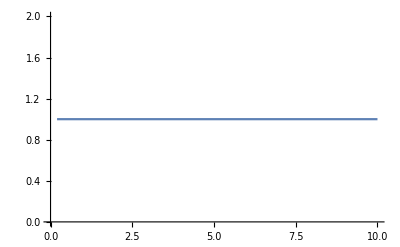

```mathematica
ListLinePlot[pPlot]
```

```mathematica
ReturnAmpLocal=FastReturnAmpMessy[HIsing,σz,17]
```

```mathematica
Select[%61//Expand]
```

0.04166666666666667 (2 (-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t)) (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))+2 (-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t)) (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))+2 (0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)-0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t)) (-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t))+(0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+5.318973070046842×10^-41 ⅇ^(-1. ⅈ t)+1.243961337076736×10^-40 ⅇ^(1. ⅈ t)-0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)-0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t)) (-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-1.243961337076736×10^-40 ⅇ^(-1. ⅈ t)-5.318973070046842×10^-41 ⅇ^(1. ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t))+(0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-5.318973070046842×10^-41 ⅇ^(-1. ⅈ t)-1.243961337076736×10^-40 ⅇ^(1. ⅈ t)-0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)-0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t)) (-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+1.243961337076736×10^-40 ⅇ^(-1. ⅈ t)+5.318973070046842×10^-41 ⅇ^(1. ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t))+(0.01729537601466939 ⅇ^(-0.1099162641747424 ⅈ t)-0.2111376428564136 ⅇ^(0.1099162641747424 ⅈ t)-0.005326604452602016 ⅇ^(-2.603875471609677 ⅈ t)+0.4408862243843599 ⅇ^(2.603875471609677 ⅈ t)+0.04181839960097069 ⅇ^(-3.493959207434934 ⅈ t)-0.2835357526909844 ⅇ^(3.493959207434934 ⅈ t)) (-0.01729537601466939 ⅇ^(0.1099162641747424 ⅈ t)+0.2111376428564136 ⅇ^(-0.1099162641747424 ⅈ t)-0.4408862243843599 ⅇ^(-2.603875471609677 ⅈ t)+0.005326604452602016 ⅇ^(2.603875471609677 ⅈ t)+0.2835357526909844 ⅇ^(-3.493959207434934 ⅈ t)-0.04181839960097069 ⅇ^(3.493959207434934 ⅈ t))-(0.01729537601466939 ⅇ^(-0.1099162641747424 ⅈ t)-0.2111376428564136 ⅇ^(0.1099162641747424 ⅈ t)-0.005326604452602016 ⅇ^(-2.603875471609677 ⅈ t)+0.4408862243843599 ⅇ^(2.603875471609677 ⅈ t)+0.04181839960097069 ⅇ^(-3.493959207434934 ⅈ t)-0.2835357526909844 ⅇ^(3.493959207434934 ⅈ t)) (0.01729537601466939 ⅇ^(0.1099162641747424 ⅈ t)-0.2111376428564136 ⅇ^(-0.1099162641747424 ⅈ t)+0.4408862243843599 ⅇ^(-2.603875471609677 ⅈ t)-0.005326604452602016 ⅇ^(2.603875471609677 ⅈ t)-0.2835357526909844 ⅇ^(-3.493959207434934 ⅈ t)+0.04181839960097069 ⅇ^(3.493959207434934 ⅈ t))-(0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-4.109325559849104×10^-40 ⅇ^(-1. ⅈ t)-2.333466915767683×10^-40 ⅇ^(1. ⅈ t)-0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)-0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-2.333466915767683×10^-40 ⅇ^(-1. ⅈ t)-4.109325559849104×10^-40 ⅇ^(1. ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)-0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)-0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t))-(0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+4.109325559849104×10^-40 ⅇ^(-1. ⅈ t)+2.333466915767683×10^-40 ⅇ^(1. ⅈ t)-0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)-0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+2.333466915767683×10^-40 ⅇ^(-1. ⅈ t)+4.109325559849104×10^-40 ⅇ^(1. ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)-0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)-0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t))-2 (0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)-0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)-0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)-0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t))-2 (-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)-0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)-0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t)) (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)+0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)+0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)+0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))-2 (-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)-0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)-0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t)) (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)+0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)+0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)+0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))-2 (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t)) (0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)+0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)-0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)-0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)+0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))-2 (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t)) (0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)+0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)-0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)-0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)+0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))+2 (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)+0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)+0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)+0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t)) (0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)+0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)+0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))+2 (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)+0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)+0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)+0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t)) (0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)+0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)+0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))+3 (-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)+0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)-0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t)) (-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)+0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)+0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t))-3 (-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t)) (-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t))+3 (-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)+0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)-0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t)) (-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)+0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)+0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t))-3 (-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t)) (-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t))+2 (0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-2 (-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)-0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)-0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))+3 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-6.34150924354049×10^-40 ⅇ^(-1. ⅈ t)-1.367315829492923×10^-41 ⅇ^(1. ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-1.367315829492923×10^-41 ⅇ^(-1. ⅈ t)-6.34150924354049×10^-40 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)-0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))+3 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+6.34150924354049×10^-40 ⅇ^(-1. ⅈ t)+1.367315829492923×10^-41 ⅇ^(1. ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+1.367315829492923×10^-41 ⅇ^(-1. ⅈ t)+6.34150924354049×10^-40 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)-0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-3 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-6.34150924354049×10^-40 ⅇ^(-1. ⅈ t)+1.367315829492923×10^-41 ⅇ^(1. ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+1.367315829492923×10^-41 ⅇ^(-1. ⅈ t)-6.34150924354049×10^-40 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-3 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+6.34150924354049×10^-40 ⅇ^(-1. ⅈ t)-1.367315829492923×10^-41 ⅇ^(1. ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-1.367315829492923×10^-41 ⅇ^(-1. ⅈ t)+6.34150924354049×10^-40 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))+3 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-1.678906271872535×10^-39 ⅇ^(-1. ⅈ t)-4.679476435350902×10^-40 ⅇ^(1. ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-4.679476435350902×10^-40 ⅇ^(-1. ⅈ t)-1.678906271872535×10^-39 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)-0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))+3 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+1.678906271872535×10^-39 ⅇ^(-1. ⅈ t)+4.679476435350902×10^-40 ⅇ^(1. ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+4.679476435350902×10^-40 ⅇ^(-1. ⅈ t)+1.678906271872535×10^-39 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)-0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-3 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-1.678906271872535×10^-39 ⅇ^(-1. ⅈ t)+4.679476435350902×10^-40 ⅇ^(1. ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+4.679476435350902×10^-40 ⅇ^(-1. ⅈ t)-1.678906271872535×10^-39 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-3 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+1.678906271872535×10^-39 ⅇ^(-1. ⅈ t)-4.679476435350902×10^-40 ⅇ^(1. ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-4.679476435350902×10^-40 ⅇ^(-1. ⅈ t)+1.678906271872535×10^-39 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-(-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+1.243961337076736×10^-40 ⅇ^(-1. ⅈ t)-5.318973070046842×10^-41 ⅇ^(1. ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)-0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)-0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+5.318973070046842×10^-41 ⅇ^(-1. ⅈ t)-1.243961337076736×10^-40 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-(-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-1.243961337076736×10^-40 ⅇ^(-1. ⅈ t)+5.318973070046842×10^-41 ⅇ^(1. ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)-0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)-0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-5.318973070046842×10^-41 ⅇ^(-1. ⅈ t)+1.243961337076736×10^-40 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))+(0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-2.333466915767683×10^-40 ⅇ^(-1. ⅈ t)+4.109325559849104×10^-40 ⅇ^(1. ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+4.109325559849104×10^-40 ⅇ^(-1. ⅈ t)-2.333466915767683×10^-40 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))+(0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+2.333466915767683×10^-40 ⅇ^(-1. ⅈ t)-4.109325559849104×10^-40 ⅇ^(1. ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-4.109325559849104×10^-40 ⅇ^(-1. ⅈ t)+2.333466915767683×10^-40 ⅇ^(1. ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))+(0.01729537601466939 ⅇ^(0.1099162641747424 ⅈ t)+0.2111376428564136 ⅇ^(-0.1099162641747424 ⅈ t)+0.4408862243843599 ⅇ^(-2.603875471609677 ⅈ t)+0.005326604452602016 ⅇ^(2.603875471609677 ⅈ t)+0.2835357526909844 ⅇ^(-3.493959207434934 ⅈ t)+0.04181839960097069 ⅇ^(3.493959207434934 ⅈ t)) (0.01729537601466939 ⅇ^(-0.1099162641747424 ⅈ t)+0.2111376428564136 ⅇ^(0.1099162641747424 ⅈ t)+0.005326604452602016 ⅇ^(-2.603875471609677 ⅈ t)+0.4408862243843599 ⅇ^(2.603875471609677 ⅈ t)+0.04181839960097069 ⅇ^(-3.493959207434934 ⅈ t)+0.2835357526909844 ⅇ^(3.493959207434934 ⅈ t))-(-0.01729537601466939 ⅇ^(0.1099162641747424 ⅈ t)-0.2111376428564136 ⅇ^(-0.1099162641747424 ⅈ t)-0.4408862243843599 ⅇ^(-2.603875471609677 ⅈ t)-0.005326604452602016 ⅇ^(2.603875471609677 ⅈ t)-0.2835357526909844 ⅇ^(-3.493959207434934 ⅈ t)-0.04181839960097069 ⅇ^(3.493959207434934 ⅈ t)) (0.01729537601466939 ⅇ^(-0.1099162641747424 ⅈ t)+0.2111376428564136 ⅇ^(0.1099162641747424 ⅈ t)+0.005326604452602016 ⅇ^(-2.603875471609677 ⅈ t)+0.4408862243843599 ⅇ^(2.603875471609677 ⅈ t)+0.04181839960097069 ⅇ^(-3.493959207434934 ⅈ t)+0.2835357526909844 ⅇ^(3.493959207434934 ⅈ t))-3 ((-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)+0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)-0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t)) (0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)-0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t))+2 (0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)-0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t))+(-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t)) (-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t))+2 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)+0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-3 (0.2111376428564136 ⅇ^(-0.1099162641747424 ⅈ t)+0.01729537601466939 ⅇ^(0.1099162641747424 ⅈ t)+0.4408862243843599 ⅇ^(-2.603875471609677 ⅈ t)+0.005326604452602016 ⅇ^(2.603875471609677 ⅈ t)+0.2835357526909844 ⅇ^(-3.493959207434934 ⅈ t)+0.04181839960097069 ⅇ^(3.493959207434934 ⅈ t)) (0.2111376428564136 ⅇ^(0.1099162641747424 ⅈ t)+0.01729537601466939 ⅇ^(-0.1099162641747424 ⅈ t)+0.005326604452602016 ⅇ^(-2.603875471609677 ⅈ t)+0.4408862243843599 ⅇ^(2.603875471609677 ⅈ t)+0.04181839960097069 ⅇ^(-3.493959207434934 ⅈ t)+0.2835357526909844 ⅇ^(3.493959207434934 ⅈ t))+3 (0.2111376428564136 ⅇ^(-0.1099162641747424 ⅈ t)-0.01729537601466939 ⅇ^(0.1099162641747424 ⅈ t)-0.4408862243843599 ⅇ^(-2.603875471609677 ⅈ t)+0.005326604452602016 ⅇ^(2.603875471609677 ⅈ t)+0.2835357526909844 ⅇ^(-3.493959207434934 ⅈ t)-0.04181839960097069 ⅇ^(3.493959207434934 ⅈ t)) (0.2111376428564136 ⅇ^(0.1099162641747424 ⅈ t)-0.01729537601466939 ⅇ^(-0.1099162641747424 ⅈ t)+0.005326604452602016 ⅇ^(-2.603875471609677 ⅈ t)-0.4408862243843599 ⅇ^(2.603875471609677 ⅈ t)-0.04181839960097069 ⅇ^(-3.493959207434934 ⅈ t)+0.2835357526909844 ⅇ^(3.493959207434934 ⅈ t)))+3 (2 (0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)-0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)-0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)-0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)-0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)+0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t))+(-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)+0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)-0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t)) (-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)+0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)+0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t))+(0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)+0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)+0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)+0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)-0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)-0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t)) (-0.06042933827250342 ⅇ^(-0.1099162641747424 ⅈ t)-0.06042933827250342 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-2.603875471609677 ⅈ t)-0.04846056671043605 ⅇ^(2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(-3.493959207434934 ⅈ t)+0.1088899049829395 ⅇ^(3.493959207434934 ⅈ t))+2 (-0.1693192432554429 ⅇ^(-0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(0.1099162641747424 ⅈ t)+0.1088899049829395 ⅇ^(-2.603875471609677 ⅈ t)+0.01196877156206737 ⅇ^(2.603875471609677 ⅈ t)+0.1573504716933755 ⅇ^(-3.493959207434934 ⅈ t)-0.06042933827250342 ⅇ^(3.493959207434934 ⅈ t)) (-0.1693192432554429 ⅇ^(0.1099162641747424 ⅈ t)-0.04846056671043605 ⅇ^(-0.1099162641747424 ⅈ t)+0.01196877156206737 ⅇ^(-2.603875471609677 ⅈ t)+0.1088899049829395 ⅇ^(2.603875471609677 ⅈ t)-0.06042933827250342 ⅇ^(-3.493959207434934 ⅈ t)+0.1573504716933755 ⅇ^(3.493959207434934 ⅈ t))-3 (0.2111376428564136 ⅇ^(-0.1099162641747424 ⅈ t)-0.01729537601466939 ⅇ^(0.1099162641747424 ⅈ t)-0.4408862243843599 ⅇ^(-2.603875471609677 ⅈ t)+0.005326604452602016 ⅇ^(2.603875471609677 ⅈ t)+0.2835357526909844 ⅇ^(-3.493959207434934 ⅈ t)-0.04181839960097069 ⅇ^(3.493959207434934 ⅈ t)) (0.2111376428564136 ⅇ^(0.1099162641747424 ⅈ t)-0.01729537601466939 ⅇ^(-0.1099162641747424 ⅈ t)+0.005326604452602016 ⅇ^(-2.603875471609677 ⅈ t)-0.4408862243843599 ⅇ^(2.603875471609677 ⅈ t)-0.04181839960097069 ⅇ^(-3.493959207434934 ⅈ t)+0.2835357526909844 ⅇ^(3.493959207434934 ⅈ t))+3 (0.2111376428564136 ⅇ^(-0.1099162641747424 ⅈ t)+0.01729537601466939 ⅇ^(0.1099162641747424 ⅈ t)+0.4408862243843599 ⅇ^(-2.603875471609677 ⅈ t)+0.005326604452602016 ⅇ^(2.603875471609677 ⅈ t)+0.2835357526909844 ⅇ^(-3.493959207434934 ⅈ t)+0.04181839960097069 ⅇ^(3.493959207434934 ⅈ t)) (0.2111376428564136 ⅇ^(0.1099162641747424 ⅈ t)+0.01729537601466939 ⅇ^(-0.1099162641747424 ⅈ t)+0.005326604452602016 ⅇ^(-2.603875471609677 ⅈ t)+0.4408862243843599 ⅇ^(2.603875471609677 ⅈ t)+0.04181839960097069 ⅇ^(-3.493959207434934 ⅈ t)+0.2835357526909844 ⅇ^(3.493959207434934 ⅈ t))))

```mathematica
ReturnAmpLocal17=FastReturnAmp[HIsing,σz,17]
```

0.04167 (0.616 ⅇ^(-0.21983252834948 ⅈ t)+0.616 ⅇ^(0.21983252834948 ⅈ t)+5.863 ⅇ^(-0.89008373582526 ⅈ t)+5.863 ⅇ^(0.89008373582526 ⅈ t)+1. ⅇ^(-2. ⅈ t)+1. ⅇ^(2. ⅈ t)+3.095 ⅇ^(-2.49395920743493 ⅈ t)+3.095 ⅇ^(2.49395920743493 ⅈ t)+1.328 ⅇ^(-3.60387547160968 ⅈ t)+1.328 ⅇ^(3.60387547160968 ⅈ t)+0.0909 ⅇ^(-5.20775094321935 ⅈ t)+0.0909 ⅇ^(5.20775094321935 ⅈ t)+0.0074 ⅇ^(-6.98791841486987 ⅈ t)+0.0074 ⅇ^(6.98791841486987 ⅈ t))

```mathematica
Simplify[N[test,2]]//Precision
```

4.02945

```mathematica
ReturnAmpLocal16=FastReturnAmp[HIsing,σz,16]
```

0.0416666666666667 (0.615991587203247 ⅇ^(-0.2198325283495 ⅈ t)+0.615991587203247 ⅇ^(0.2198325283495 ⅈ t)+5.86276915818345 ⅇ^(-0.8900837358253 ⅈ t)+5.86276915818345 ⅇ^(0.8900837358253 ⅈ t)+1. ⅇ^(-2. ⅈ t)+1. ⅇ^(2. ⅈ t)+3.09493215864349 ⅇ^(-2.4939592074349 ⅈ t)+3.09493215864349 ⅇ^(2.4939592074349 ⅈ t)+1.32801296888735 ⅇ^(-3.6038754716097 ⅈ t)+1.32801296888735 ⅇ^(3.6038754716097 ⅈ t)+0.0908519722822266 ⅇ^(-5.2077509432194 ⅈ t)+0.0908519722822266 ⅇ^(5.2077509432194 ⅈ t)+0.007442154800241 ⅇ^(-6.9879184148699 ⅈ t)+0.007442154800241 ⅇ^(6.9879184148699 ⅈ t))

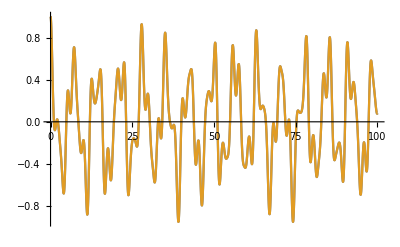

```mathematica
Plot[{ReturnAmpLocal16,ReturnAmpLocal17},{t,0,100}]
```

```mathematica
ReturnAmpLocal=FastReturnAmp[HIsing,σz,15]
```

0.61599158720325 ⅇ^(-0.219832528349 ⅈ t)+0.61599158720325 ⅇ^(0.219832528349 ⅈ t)+5.8627691581835 ⅇ^(-0.890083735825 ⅈ t)+5.8627691581835 ⅇ^(0.890083735825 ⅈ t)+1. ⅇ^(-2. ⅈ t)+1. ⅇ^(2. ⅈ t)+3.0949321586435 ⅇ^(-2.493959207435 ⅈ t)+3.0949321586435 ⅇ^(2.493959207435 ⅈ t)+1.3280129688873 ⅇ^(-3.60387547161 ⅈ t)+1.3280129688873 ⅇ^(3.60387547161 ⅈ t)+0.090851972282227 ⅇ^(-5.207750943219 ⅈ t)+0.090851972282227 ⅇ^(5.207750943219 ⅈ t)+0.007442154800241 ⅇ^(-6.98791841487 ⅈ t)+0.007442154800241 ⅇ^(6.98791841487 ⅈ t)

0.041666666666667 (0.61599158720325 ⅇ^(-0.219832528349 ⅈ t)+0.61599158720325 ⅇ^(0.219832528349 ⅈ t)+5.8627691581835 ⅇ^(-0.890083735825 ⅈ t)+5.8627691581835 ⅇ^(0.890083735825 ⅈ t)+1. ⅇ^(-2. ⅈ t)+1. ⅇ^(2. ⅈ t)+3.0949321586435 ⅇ^(-2.493959207435 ⅈ t)+3.0949321586435 ⅇ^(2.493959207435 ⅈ t)+1.3280129688873 ⅇ^(-3.60387547161 ⅈ t)+1.3280129688873 ⅇ^(3.60387547161 ⅈ t)+0.090851972282227 ⅇ^(-5.207750943219 ⅈ t)+0.090851972282227 ⅇ^(5.207750943219 ⅈ t)+0.007442154800241 ⅇ^(-6.98791841487 ⅈ t)+0.007442154800241 ⅇ^(6.98791841487 ⅈ t))

```mathematica
{as,bs}=LanczosOrthog[HIsing,σz,15,20]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{2.,2.309401076758503058,2.943920288775948952,3.941885530867371402,4.069465365687311086,3.65847424585976449,3.750002195508072836,3.014734931008532551,2.88220253272860873,0.8727753285277059179,1.53175826497057184,1.358742054494604503,0.322678716559696877}}

```mathematica
PTabLocal=AmplitudeCoefficient[as,bs,ReturnAmpLocal,tVals,Prec];
```

```mathematica
PTabLocal[[1,3]]
```

0.084386106045+0. ⅈ

```mathematica
pPlot=Table[{tVals[[j]],Sum[  Abs[PTabLocal[[k, j]]^2 ] , {k, 1, Length[PTabLocal]} ] }, {j, 1, Length[tVals]}];
```

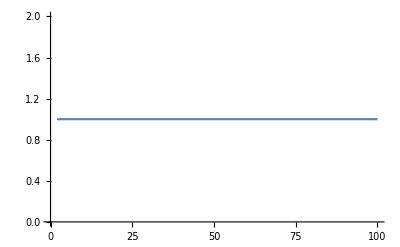

```mathematica
ListLinePlot[pPlot,PlotRange->All]
```

### Local Op

```mathematica
ReturnAmpLocal=ExactReturnAmp[HIsing,σy]
```

ExactReturnAmp[{{-1,-1,-1,0},{-1,1,0,-1},{-1,0,1,-1},{0,-1,-1,-1}},{{0,-ⅈ,-ⅈ,0},{ⅈ,0,0,-ⅈ},{ⅈ,0,0,-ⅈ},{0,ⅈ,ⅈ,0}}]

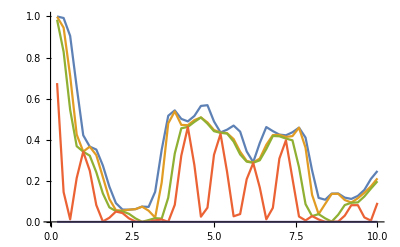

```mathematica
PPlot= Table[Table[{tVals[[j]],Sum[  Abs[PTabLocal[[k, j]]^2 ] , {k, 1, Length[PTabLocal]-m} ] }, {j, 1, Length[tVals]}],{m,0,4}];
ListLinePlot[PPlot, PlotRange->{0,Automatic}]
```

```mathematica
ReturnAmpSx=FasterReturnAmp[HIsing,σx,10,10^-9]
```

0.04166667 (17.14286+0.1851558 Cos[2.713792 t]+4.719912 Cos[3.384043 t]+1.952075 Cos[6.097835 t]+0. Sin[2.713792 t]+0. Sin[3.384043 t]+0. Sin[6.097835 t])

```mathematica
{as,bs}=LanczosOrthog[HIsing,σx,5,20]
```

{{0.,0.,0.,0.},{2.309401076758503058,4.546060565661951964,2.816999089628490089}}

```mathematica
PTabLocal=AmplitudeCoefficient[as,bs,ReturnAmpSx,tVals,Prec];
```

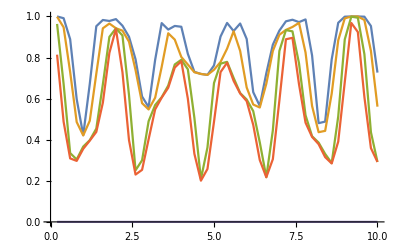

```mathematica
PPlot= Table[Table[{tVals[[j]],Sum[  Abs[PTabLocal[[k, j]]^2 ] , {k, 1, Length[PTabLocal]-m} ] }, {j, 1, Length[tVals]}],{m,0,4}];
ListLinePlot[PPlot, PlotRange->{0,Automatic}]
```

```mathematica
(*Notes
σy produces a total probability of 2.5, lines are jagged ---- check for conjugation.
σxMode[3] Produces errors, as Lanczos algorithm terminates early. ---- check Boundary Condition implementation.

Speed up - diagonalize the hamiltonian, use to contruct U. not sure if its U^+H U or U H U^+ check ordering of the eigenvectors in the matrix output of Eigensystem[].
*)
```

### Fermionic Creation operator (J-W string)

```mathematica
ReturnAmpNonLocal=Abs[FasterReturnAmp[HIsing,ccc,10,10^-9]]
```

0.08333333 Abs[1.142857+0.1920042 Cos[0.219833 t]+1.241151 Cos[0.890084 t]+1. Cos[1.10992 t]+1. Cos[1.60388 t]+1.849701 Cos[2.493959 t]+0.7662909 Cos[2.713792 t]+0.2411513 Cos[3.384043 t]+1.766291 Cos[3.603875 t]+1. Cos[4.493959 t]+0.454574 Cos[5.207751 t]+0.8497007 Cos[6.097835 t]+0.4962789 Cos[6.987918 t]+0.1874202 ⅈ Sin[0.219833 t]-0.7959696 ⅈ Sin[0.890084 t]+0.8711192 ⅈ Sin[1.10992 t]+0.4834347 ⅈ Sin[1.60388 t]-0.5045391 ⅈ Sin[2.493959 t]+0.6419942 ⅈ Sin[2.713792 t]-0.2291251 ⅈ Sin[3.384043 t]+0.8628591 ⅈ Sin[3.603875 t]-0.3876845 ⅈ Sin[4.493959 t]+0.3377195 ⅈ Sin[5.207751 t]-0.1585595 ⅈ Sin[6.097835 t]-0.4211293 ⅈ Sin[6.987918 t]]

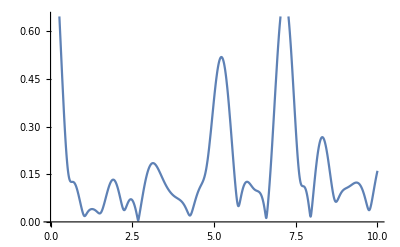

```mathematica
Plot[ReturnAmpNonLocal,{t,0,10}]
```

```mathematica
{as,bs}=LanczosOrthog[HIsing,ccc,10,20]
```

{{0.,0.941176470588235294,0.382640956797656822,0.030274229207705124,-0.050233539118449735,0.085383349759466205,-0.377693131789385838,-0.189524874596044526,-0.43023857096052693},{3.366501646120692651,3.728069282712067402,3.732135477147001127,3.476290812366388628,3.369228715623657075,3.802006563266974192,3.667429578386479907,3.438449414340386029}}

```mathematica
PTabNonLocal=AmplitudeCoefficient[as,bs,ReturnAmpNonLocal,tVals,Prec];
```

```mathematica
PPlot= Table[Table[{tVals[[j]],Sum[  Abs[PTabNonLocal[[k, j]]^2 ] , {k, 1, Length[PTabNonLocal]-m} ] }, {j, 1, Length[tVals]}],{m,0,4}];
ListLinePlot[PPlot, PlotRange->{0,Automatic}]
```

-Graphics-

### Very local operator

```mathematica
LocalOp=σxMode[2];
```

```mathematica
LocalOp//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
comm[HIsing,LocalOp]//MatrixForm
```

(0 | 0 | 0 | 0 | -2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 | 0 | 0 | 0 | 0)

```mathematica
ReturnAmpLocal=NormalizedReturnAmplitude[HIsing,LocalOp]
```

$Aborted

```mathematica
{as,bs}=LanczosOrthog[HIsing,LocalOp,10,20]
```

{{0.,0.,0.,0,0,0,0,0,0},{2.828427124746190098,2.828427124746190098,0,0,0,0,0,0}}

```mathematica
PTabLocal=AmplitudeCoefficient[as,bs,ReturnAmpLocal,tVals,Prec];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
PPlot= Table[Table[{tVals[[j]],Sum[  Abs[PTabLocal[[k, j]]^2 ] , {k, 1, Length[PTabLocal]-m} ] }, {j, 1, Length[tVals]}],{m,0,4}];
ListLinePlot[PPlot, PlotRange->{0,Automatic}]
```

-Graphics-

### Weird non-local operator

```mathematica
WeirdOp=σxMode[1].σyMode[3]+σyMode[1]+σyMode[3];
```

```mathematica
WeirdOp//MatrixForm
```

(0 | -ⅈ | 0 | 0 | -ⅈ | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | -ⅈ
0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | -ⅈ
ⅈ | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0
ⅈ | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | ⅈ | 0 | 0 | ⅈ | 0)

```mathematica
ReturnAmpWeird=NormalizedReturnAmplitude[HIsing,WeirdOp]
```

Cos[2 t]^2

```mathematica
{as,bs}=LanczosOrthog[HIsing,WeirdOp,10,20]
```

{{0.,0.,0.,0,0,0,0,0,0},{2.828427124746190098,2.828427124746190098,0,0,0,0,0,0}}

```mathematica
PTabWeird=AmplitudeCoefficient[as,bs,ReturnAmpWeird,tVals,Prec];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

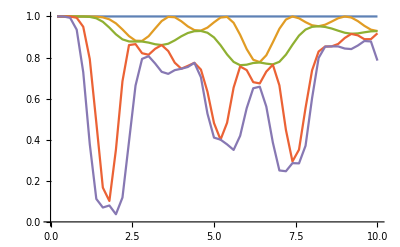

```mathematica
PPlot= Table[Table[{tVals[[j]],Sum[  Abs[PTabWeird[[k, j]]^2 ] , {k, 1, Length[PTabWeird]-m} ] }, {j, 1, Length[tVals]}],{m,0,4}];
ListLinePlot[PPlot, PlotRange->{0,Automatic}]
```

### Random entries operator

```mathematica
RanOp=Table[Random[],{i,1,8},{j,1,8}];
```

```mathematica
ReturnAmpRan=NormalizedReturnAmplitude[HIsing,RanOp]
```

(0.0576983+0. ⅈ) (9.87295+7.45859 Cos[4 t]-(0.+0.319764 ⅈ) Sin[4 t])

```mathematica
{as,bs}=LanczosOrthog[HIsing,RanOp,10,20]
```

{{-0.0737993,-0.0239663,0.0977655,0.,0.,0.,0.,0.,0.},{2.623,3.01862,0.,0.,0.,0.,0.,0.}}

```mathematica
PTabRan=AmplitudeCoefficient[as,bs,ReturnAmpRan,tVals,Prec];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
PPlot= Table[Table[{tVals[[j]],Sum[  Abs[PTabRan[[k, j]]^2 ] , {k, 1, Length[PTabRan]-m} ] }, {j, 1, Length[tVals]}],{m,0,4}];
ListLinePlot[PPlot, PlotRange->{0,Automatic}]
```

-Graphics-

Check for analytic expr for return amp
Use moments method to calc return amp.

```mathematica
y=2 (0.13578349056445850901686445139338893222`16.69897000433602 ⅇ^(-0.10991626417474238284438974201282096213`16.30102999566398 ⅈ t)-0.13578349056445850901686445139338893222`16.69897000433602 ⅇ^(0.10991626417474238284438974201282096213`16.30102999566398 ⅈ t)+0.25`16.69897000433602 ⅇ^(-1.`16.30102999566398 ⅈ t)-0.25`16.69897000433602 ⅇ^(1.`16.30102999566398 ⅈ t)-0.02689358558151903353392822257112572781`16.69897000433602 ⅇ^(-2.60387547160967650494440927802978020466`16.30102999566398 ⅈ t)+0.02689358558151903353392822257112572781`16.69897000433602 ⅇ^(2.60387547160967650494440927802978020466`16.30102999566398 ⅈ t)+0.08732292385402245744920732603548533996`16.69897000433602 ⅇ^(-3.49395920743493412210001953601695924253`16.301029995663978 ⅈ t)-0.08732292385402245744920732603548533996`16.69897000433602 ⅇ^(3.49395920743493412210001953601695924253`16.301029995663978 ⅈ t))^2+2 (0.13578349056445850901686445139338893222`16.69897000433602 ⅇ^(-0.10991626417474238284438974201282096213`16.30102999566398 ⅈ t)-0.13578349056445850901686445139338893222`16.69897000433602 ⅇ^(0.10991626417474238284438974201282096213`16.30102999566398 ⅈ t)-0.25`16.69897000433602 ⅇ^(-1.`16.30102999566398 ⅈ t)+0.25`16.69897000433602 ⅇ^(1.`16.30102999566398 ⅈ t)-0.02689358558151903353392822257112572781`16.69897000433602 ⅇ^(-2.60387547160967650494440927802978020466`16.30102999566398 ⅈ t)+0.02689358558151903353392822257112572781`16.69897000433602 ⅇ^(2.60387547160967650494440927802978020466`16.30102999566398 ⅈ t)+0.08732292385402245744920732603548533996`16.69897000433602 ⅇ^(-3.49395920743493412210001953601695924253`16.301029995663978 ⅈ t)-0.08732292385402245744920732603548533996`16.69897000433602 ⅇ^(3.49395920743493412210001953601695924253`16.301029995663978 ⅈ t))^2
```

2 (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))^2+2 (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))^2

```mathematica
2 (0.13578349056445850901686445139338893222`16.69897000433602 ⅇ^(-0.10991626417474238284438974201282096213`16.30102999566398 ⅈ t)-0.13578349056445850901686445139338893222`16.69897000433602 ⅇ^(0.10991626417474238284438974201282096213`16.30102999566398 ⅈ t)+0.25`16.69897000433602 ⅇ^(-1.`16.30102999566398 ⅈ t)-0.25`16.69897000433602 ⅇ^(1.`16.30102999566398 ⅈ t)-0.02689358558151903353392822257112572781`16.69897000433602 ⅇ^(-2.60387547160967650494440927802978020466`16.30102999566398 ⅈ t)+0.02689358558151903353392822257112572781`16.69897000433602 ⅇ^(2.60387547160967650494440927802978020466`16.30102999566398 ⅈ t)+0.08732292385402245744920732603548533996`16.69897000433602 ⅇ^(-3.49395920743493412210001953601695924253`16.301029995663978 ⅈ t)-0.08732292385402245744920732603548533996`16.69897000433602 ⅇ^(3.49395920743493412210001953601695924253`16.301029995663978 ⅈ t))^2+2 (0.13578349056445850901686445139338893222`16.69897000433602 ⅇ^(-0.10991626417474238284438974201282096213`16.30102999566398 ⅈ t)-0.13578349056445850901686445139338893222`16.69897000433602 ⅇ^(0.10991626417474238284438974201282096213`16.30102999566398 ⅈ t)-0.25`16.69897000433602 ⅇ^(-1.`16.30102999566398 ⅈ t)+0.25`16.69897000433602 ⅇ^(1.`16.30102999566398 ⅈ t)-0.02689358558151903353392822257112572781`16.69897000433602 ⅇ^(-2.60387547160967650494440927802978020466`16.30102999566398 ⅈ t)+0.02689358558151903353392822257112572781`16.69897000433602 ⅇ^(2.60387547160967650494440927802978020466`16.30102999566398 ⅈ t)+0.08732292385402245744920732603548533996`16.69897000433602 ⅇ^(-3.49395920743493412210001953601695924253`16.301029995663978 ⅈ t)-0.08732292385402245744920732603548533996`16.69897000433602 ⅇ^(3.49395920743493412210001953601695924253`16.301029995663978 ⅈ t))^2
```

2 (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)+0.25 ⅇ^(-1. ⅈ t)-0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))^2+2 (0.1357834905644585 ⅇ^(-0.1099162641747424 ⅈ t)-0.1357834905644585 ⅇ^(0.1099162641747424 ⅈ t)-0.25 ⅇ^(-1. ⅈ t)+0.25 ⅇ^(1. ⅈ t)-0.02689358558151903 ⅇ^(-2.603875471609677 ⅈ t)+0.02689358558151903 ⅇ^(2.603875471609677 ⅈ t)+0.08732292385402246 ⅇ^(-3.493959207434934 ⅈ t)-0.08732292385402246 ⅇ^(3.493959207434934 ⅈ t))^2

```mathematica
2 (0.13578349056445851 E^(-0.10991626417474238 I t)-0.13578349056445851 E^(0.10991626417474238 I t)+0.25000000000000000 E^(-1.0000000000000000 I t)-0.25000000000000000 E^(1.0000000000000000 I t)-0.026893585581519034 E^(-2.603875471609677 I t)+0.026893585581519034 E^(2.603875471609677 I t)+0.08732292385402246 E^(-3.493959207434934 I t)-0.08732292385402246 E^(3.493959207434934 I t))^2+2 (0.13578349056445851 E^(-0.10991626417474238 I t)-0.13578349056445851 E^(0.10991626417474238 I t)-0.25000000000000000 E^(-1.0000000000000000 I t)+0.25000000000000000 E^(1.0000000000000000 I t)-0.026893585581519034 E^(-2.603875471609677 I t)+0.026893585581519034 E^(2.603875471609677 I t)+0.08732292385402246 E^(-3.493959207434934 I t)-0.08732292385402246 E^(3.493959207434934 I t))^2
```

2 (0.135783 ⅇ^((0.-0.109916 ⅈ) t)-0.135783 ⅇ^((0.+0.109916 ⅈ) t)+0.25 ⅇ^((0.-1. ⅈ) t)-0.25 ⅇ^((0.+1. ⅈ) t)-0.0268936 ⅇ^((0.-2.60388 ⅈ) t)+0.0268936 ⅇ^((0.+2.60388 ⅈ) t)+0.0873229 ⅇ^((0.-3.49396 ⅈ) t)-0.0873229 ⅇ^((0.+3.49396 ⅈ) t))^2+2 (0.135783 ⅇ^((0.-0.109916 ⅈ) t)-0.135783 ⅇ^((0.+0.109916 ⅈ) t)-0.25 ⅇ^((0.-1. ⅈ) t)+0.25 ⅇ^((0.+1. ⅈ) t)-0.0268936 ⅇ^((0.-2.60388 ⅈ) t)+0.0268936 ⅇ^((0.+2.60388 ⅈ) t)+0.0873229 ⅇ^((0.-3.49396 ⅈ) t)-0.0873229 ⅇ^((0.+3.49396 ⅈ) t))^2

```mathematica
Ny=N[y]
```

-5.39814 x^2+1.77245 x^3

```mathematica
Simplify[Ny]
```

x^2 (-5.39814+1.77245 x)

```mathematica
Simplify[N[y,15]]
```

x^2 (-5.39814156908377+1.77245385090552 x)

```mathematica
Simplify[N[y,16]]
```

x^2 (-5.39814156908377+1.77245385090552 x)

```mathematica
Simplify[N[y,17]]
```

x^2 (-5.39814156908377+1.77245385090552 x)